# Exploring Food Data

Corwin Kerr

The Wolfram Language has a built-in knowledge base to feed WolframAlpha. I was curious about exploring the data associated with food and ended up exploring smoothie drink colors.

## What data is available?

Free form input can be used to start the search for available data:

```mathematica
strawberry=LinguisticAssistant
```

And see what this is behind the scenes:

```mathematica
%//InputForm
```

Entity["Food", {EntityProperty["Food", "FoodType"] -> 
   ContainsExactly[{Entity["FoodType", "Strawberry"]}], 
  EntityProperty["Food", "AddedFoodTypes"] -> ContainsExactly[{}]}]

There is a difference between Food, FoodType, and FoodTypeGroup. “Food” has the most properties that we can query.

```mathematica
{foodProperties,foodTypeProperties,foodTypeGroupProperties}=EntityProperties[#]&/@{"Food","FoodType","FoodTypeGroup"};
Length/@%
```

{627,32,12}

### The Role of FoodTypeGroup

We can see the 31 FoodTypeGroup which are available.

```mathematica
foodTypeGroup=EntityValue["FoodTypeGroup","Entities"]
```

{alcoholic beverages,berries,breads,candies,carbonated beverages,cheeses,coffee beverages,drinks,fats,fishes,frozen novelties,fruits,greens,juices,meats,milks,nuts,oils,pastas,plants,poultry,preserves,roes,sandwiches,sauces,seafood,seeds,soups,soy,spices,squashes}

Some contain more elements than others...

```mathematica
Length/@EntityValue[foodTypeGroup,"Foods"]
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

{646,86,1232,1825,415,633,1,2802,347,1093,613,6131,209,1190,1,1872,1185,1319,1377,2676,6,149,39,283,1009,1,5137,1050,72,3,288}

## Making a Smoothie

Say we are interested in making a smoothie, and we need to understand the densities of fruits we pick.

```mathematica
foodTypesOfInterest={Entity["FoodTypeGroup","Fruits"],Entity["FoodTypeGroup","Greens"],Entity["FoodTypeGroup","Juices"]};
```

We can define a function to get densities of food types, being careful to ignore the foods with missing values.

```mathematica
densityOfFoodType[type_]:=EntityValue[EntityValue[type["Foods"]],"Density","NonMissingEntityAssociation"]
SetAttributes[densityOfFoodType,Listable]
```

```mathematica
densityOfFoodType[Entity["FoodTypeGroup","Greens"]]
```

<|Beet greens, cooked, boiled, drained, without salt→0.608652 g/cm^3,Beet greens, cooked, boiled, drained, with salt→0.608652 g/cm^3,Beet greens, raw→0.160617 g/cm^3,Chicory greens, raw→0.122576 g/cm^3,Collards, cooked, boiled, drained, without salt→0.760816 g/cm^3,Collards, cooked, boiled, drained, with salt→0.760816 g/cm^3,Collards, frozen, chopped, cooked, boiled, drained, without salt→0.760816 g/cm^3,Collards, frozen, chopped, cooked, boiled, drained, with salt→0.760816 g/cm^3,Collards, frozen, chopped, unprepared→0.760816 g/cm^3,Collards, raw→0.152163 g/cm^3,Dandelion greens, cooked, boiled, drained, without salt→0.443809 g/cm^3,Dandelion greens, cooked, boiled, drained, with salt→0.443809 g/cm^3,Dandelion greens, raw→0.232471 g/cm^3,Mustard greens, cooked, boiled, drained, without salt→0.614288 g/cm^3,Mustard greens, frozen, cooked, boiled, drained, without salt→0.614288 g/cm^3,Mustard greens, frozen, unprepared→0.614288 g/cm^3,Mustard greens, raw→0.236698 g/cm^3,Pumpkin leaves, cooked, boiled, drained, without salt→0.300099 g/cm^3,Pumpkin leaves, cooked, boiled, drained, with salt→0.300099 g/cm^3,Pumpkin leaves, raw→0.164843 g/cm^3,Spices, bay leaf→0.12173 g/cm^3,Turnip greens, canned, no salt added→0.98906 g/cm^3,Turnip greens, canned, solids and liquids→0.98906 g/cm^3,Turnip greens, cooked, boiled, drained, without salt→0.98906 g/cm^3,Turnip greens, frozen, cooked, boiled, drained, without salt→0.98906 g/cm^3,Turnip greens, frozen, unprepared→0.98906 g/cm^3,Turnip greens, raw→0.232471 g/cm^3|>

We generate a list of associations with one element each for our foods of interest.

```mathematica
den=densityOfFoodType[foodTypesOfInterest];
```

We can visualize the density of fruits.

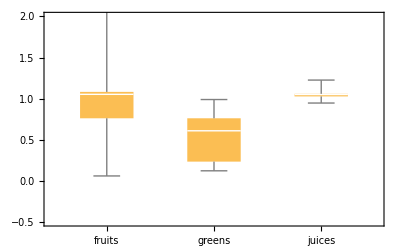

```mathematica
BoxWhiskerChart[den,PlotRange->{-.5,2},ChartLabels->{"fruits","greens","juices"}]
```

It looks like greens tend to be much less dense, but what is the fruit with the ridiculous density?  Here are the outlying fruit items, which have a density greater than that of lead (11.34 "g""/"("cm")^3)! This must be an error.

```mathematica
Select[den[[1]],#>Entity["Element","Lead"][EntityProperty["Element","Density"]]&]
```

<|PREGO Pasta, Chunky Garden Tomato, Onion and Garlic Italian Sauce, ready-to-serve→17.5833 g/cm^3,PREGO Pasta, Tomato, Basil and Garlic Italian Sauce, ready-to-serve→17.5833 g/cm^3|>

## Fruit Color Space

I decided to investigate the colors of smoothies one could make from different kinds of ingredients.

```mathematica
insideColorsetOfFoodType[type_]:=EntityValue[type,"TypicalInsideColors"]
SetAttributes[insideColorsetOfFoodType,Listable]
```

```mathematica
outsideColorsetOfFoodType[type_]:=EntityValue[type,"TypicalOutsideColors"]
SetAttributes[outsideColorsetOfFoodType,Listable]
```

```mathematica
rgbFromColorset[set_]:=EntityValue[set,EntityProperty["ColorSet","TypicalColorValue"]]
```

Apples have certain exterior colors given as names:

```mathematica
outsideColorsetOfFoodType[]
```

{brown,cream,green,red,white,yellow}

We get representative instances of these colors.

```mathematica
rgbFromColorset@%
```

{RGBColor[0.6, 0.4, 0.2],RGBColor[1., 0.992157, 0.815686],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 1],RGBColor[1, 1, 0]}

Note that we can also see their interior colors, which aren’t quite as pretty.

```mathematica
rgbFromColorset@insideColorsetOfFoodType[]
```

{RGBColor[0.6, 0.4, 0.2],RGBColor[1., 0.992157, 0.815686],RGBColor[1, 1, 1],RGBColor[1, 1, 0]}

Generate a 3D span of the exterior in XYZ color space and display it in 2D color space:

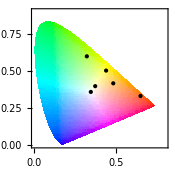

```mathematica
ChromaticityPlot[rgbFromColorset[outsideColorsetOfFoodType[]],PlotStyle->Black]
```

Define functions to generate instances of possible fruit colors based on its exterior colors .

```mathematica
fruitColorList[fruit_]:=List@@@ColorConvert[rgbFromColorset[outsideColorsetOfFoodType[fruit]],"XYZ"]
fruitInsideColorList[fruit_]:=List@@@ColorConvert[rgbFromColorset[insideColorsetOfFoodType[fruit]],"XYZ"]
fruitColorHull[fruit_]:=ConvexHullMesh[fruitColorList[fruit]]
```

Here we generate a lot of possible apple colors by picking random points within the color space.

```mathematica
applecolors=XYZColor@@@RandomPoint[fruitColorHull[],100]
```

{XYZColor[0.911466337041874, 0.9473902661537997, 0.7455627764549667],XYZColor[0.5968850135434437, 0.6129310811834142, 0.3114023806206675],XYZColor[0.5666720163812377, 0.7986606923574012, 0.19701348182348144],XYZColor[0.697360896967444, 0.7201656762718526, 0.10386745657197682],XYZColor[0.6588923658707154, 0.5882536268670421, 0.2663172147992833],XYZColor[0.6627718333501852, 0.7145194321227327, 0.33779641429219887],XYZColor[0.6522180582442659, 0.6336723041098812, 0.17844387653733385],XYZColor[0.7232190788586642, 0.8059025188534096, 0.1281959310833991],XYZColor[0.39049322134623254, 0.35532037648391623, 0.1400510120593399],XYZColor[0.5559284583844514, 0.5038953836332923, 0.3063870094871103],XYZColor[0.5803256825482196, 0.7107491967421892, 0.34408659397965924],XYZColor[0.5813122447920999, 0.5137928570681479, 0.14295518668391738],XYZColor[0.5016787249945655, 0.551588763218617, 0.1015747471568137],XYZColor[0.5314835470362461, 0.46134932471155865, 0.0643680976724168],XYZColor[0.5351452039249253, 0.5194066240793153, 0.3249197799903142],XYZColor[0.6895093093066856, 0.6438998548173335, 0.37152769223250337],XYZColor[0.44694864260299705, 0.7269620688804198, 0.09837419009905446],XYZColor[0.343236530153034, 0.25655326483055796, 0.045388029287305676],XYZColor[0.36426618069485883, 0.5141441759427964, 0.0777761237875707],XYZColor[0.5186035658849896, 0.5261652010458803, 0.3332606730150903],XYZColor[0.8056705281567832, 0.8588639611870575, 0.374526791571152],XYZColor[0.5949284046171496, 0.7628265697991835, 0.3191027474425253],XYZColor[0.6644700603621175, 0.6442514228077426, 0.3552538990813833],XYZColor[0.6761562971244927, 0.8252982028442549, 0.24656647832527112],XYZColor[0.7661470355774834, 0.7429812292124919, 0.4396142661125867],XYZColor[0.6948319833749238, 0.6999340691063322, 0.2827960291193369],XYZColor[0.5943141507370188, 0.7054062525716486, 0.3525208944902968],XYZColor[0.3453528019714134, 0.5407178257118425, 0.08306295804074959],XYZColor[0.4656100878568551, 0.4760912405236698, 0.06914726359395951],XYZColor[0.7861311919712425, 0.8495795421298246, 0.3598058344951359],XYZColor[0.457134596405785, 0.5920618146458675, 0.22951954202794356],XYZColor[0.6542940614349438, 0.5962182136400219, 0.31192373699032017],XYZColor[0.46935278033219296, 0.7245759786224178, 0.10716847272623242],XYZColor[0.6411990305940577, 0.8205020880991613, 0.18267106866323612],XYZColor[0.49752992769838145, 0.5531972873134404, 0.09624295767657531],XYZColor[0.6806809260838159, 0.7864314409490768, 0.15324227808270907],XYZColor[0.37675443763962235, 0.2838837158369413, 0.07578577693902788],XYZColor[0.5264204638808688, 0.6223265498623202, 0.17608429400923464],XYZColor[0.5440907264601279, 0.5028249895881475, 0.32436875243568364],XYZColor[0.5033228932557495, 0.40364478440144713, 0.19572600541667406],XYZColor[0.8152556102019678, 0.9136708852631062, 0.6283170536619759],XYZColor[0.506540406700018, 0.7150596200656248, 0.12029775955802502],XYZColor[0.3377848200648572, 0.292332784012317, 0.05526132622590263],XYZColor[0.6207866939075074, 0.6471680436657391, 0.08518775581287197],XYZColor[0.7355680172551616, 0.8435189534680795, 0.4572052474446927],XYZColor[0.7836855946138873, 0.8034951135853453, 0.5709483316246476],XYZColor[0.5134763743819443, 0.36771745746712614, 0.15709272540928687],XYZColor[0.5062936055811623, 0.6670132104958361, 0.13641587707171976],XYZColor[0.5420103021383177, 0.5125576547035556, 0.07076362618399767],XYZColor[0.6871051834735001, 0.697113684033479, 0.4903212634717683],XYZColor[0.6635149064376916, 0.6506432244781638, 0.11315958141062976],XYZColor[0.5041502686196296, 0.5034868985284017, 0.2716500632125848],XYZColor[0.47301377489757634, 0.698177039812866, 0.18174671252090302],XYZColor[0.7000852214364605, 0.7010381018159909, 0.22553508843304104],XYZColor[0.22397380419075963, 0.23325275463638884, 0.05439585144882686],XYZColor[0.641553746491759, 0.7472282379046834, 0.12022744062675839],XYZColor[0.414907471443446, 0.7143413573606286, 0.13535918651951995],XYZColor[0.581875210279759, 0.5361972110963632, 0.1593911822677595],XYZColor[0.5181953709085295, 0.6053261719800377, 0.1721310047836626],XYZColor[0.4940122771950187, 0.5801684225492373, 0.13768957681921923],XYZColor[0.44928338230837983, 0.4577471373949288, 0.2523494696526535],XYZColor[0.6434379713942066, 0.6798827277771203, 0.3123964205904336],XYZColor[0.664365334579554, 0.8236507694800045, 0.39554489531785786],XYZColor[0.3974990221323512, 0.5671545509662553, 0.1306011540032379],XYZColor[0.7331226937201564, 0.8451173247924096, 0.22357328039348345],XYZColor[0.8071135482177408, 0.8781258360369085, 0.5708271413506799],XYZColor[0.5289889918213354, 0.7347977304539565, 0.2158212509469276],XYZColor[0.5473312399346827, 0.5398562769541365, 0.3577865931635763],XYZColor[0.7672846397079048, 0.8686769391248875, 0.32938274018877023],XYZColor[0.4967384577410371, 0.4680799411853963, 0.10493634573043964],XYZColor[0.8706854582801252, 0.9376163826244196, 0.5287945482075754],XYZColor[0.5604875638376149, 0.6598895304858389, 0.3545017257527908],XYZColor[0.5640329343998466, 0.5649321875611243, 0.3804512279271114],XYZColor[0.4856877080596248, 0.7175353270826471, 0.18846275839894977],XYZColor[0.5685340839034626, 0.5930228992612808, 0.39403292969197923],XYZColor[0.5321929508301787, 0.523904135138101, 0.18287269141323892],XYZColor[0.699498280650736, 0.8380076950003562, 0.35431137368789545],XYZColor[0.4912806755447542, 0.4532651922433085, 0.22722991488240563],XYZColor[0.7782246032674133, 0.8554351308811236, 0.397979660418997],XYZColor[0.4225972002926901, 0.5916051641801888, 0.10384862317117305],XYZColor[0.7326253931588639, 0.868695738217245, 0.2250550446556837],XYZColor[0.3914476510816235, 0.41808333798025565, 0.18012356577470134],XYZColor[0.42251636052832164, 0.49164263107305095, 0.15733879812330154],XYZColor[0.45980855900407513, 0.753754334607074, 0.1706390439851967],XYZColor[0.4102368734410815, 0.40746001849239455, 0.16322636948881764],XYZColor[0.8851247091530491, 0.9458667342829409, 0.5919162605321034],XYZColor[0.8269036930595283, 0.9292327275100446, 0.21236453098463548],XYZColor[0.7011696396429136, 0.8572424474917625, 0.4962434878088472],XYZColor[0.5462230003965455, 0.5377848605637684, 0.20172335035550903],XYZColor[0.568743235359017, 0.6659561776604349, 0.14563053983521423],XYZColor[0.29598976403559896, 0.4067663263952902, 0.06844891046310209],XYZColor[0.5605214744531254, 0.6536119001332185, 0.35068003372130174],XYZColor[0.7400522782737181, 0.7548207126215435, 0.4132190535406527],XYZColor[0.43791601256797386, 0.6619817050039399, 0.1452602461641267],XYZColor[0.3590491302583456, 0.3305760101300891, 0.1755953195321983],XYZColor[0.4539648762116514, 0.5335989455758122, 0.07580927210210708],XYZColor[0.7396116632516646, 0.8375212700324256, 0.21044906308815714],XYZColor[0.6100582136849017, 0.6568006798746456, 0.23696003545801025],XYZColor[0.7617233466839989, 0.8085298886336804, 0.5783388367255958],XYZColor[0.7961957674672892, 0.9205094419368139, 0.19657258683224943]}

And visualize them in 3D and 2D space:

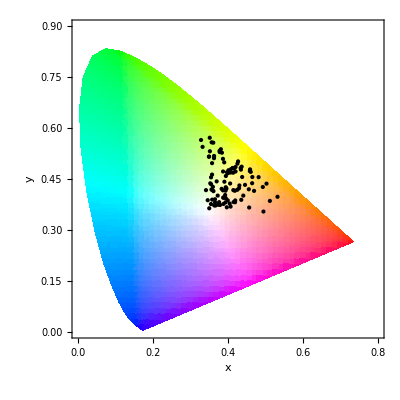
-Graphics3D-
-Graphics-

```mathematica
{ChromaticityPlot3D[#],ChromaticityPlot[#,PlotStyle->Black]}&[applecolors]//TableForm
```

To visualize the possible colors in a combination of fruits, we combine the color lists of our fruits of interest. I’m using Interpreter to get the entities for the string inputs.

```mathematica
cols=fruitColorList[Interpreter["Food"][#]]&/@{"Apple","Orange","Carrot","Banana","Blueberry","Blackberry","Strawberry"};
XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],100]
```

{XYZColor[0.7353543070876257, 0.8583149454004094, 0.19950110500712148],XYZColor[0.3505316447605792, 0.2082174340089441, 0.3554737183964668],XYZColor[0.7150746303703884, 0.7872467658850121, 0.582676916593497],XYZColor[0.3587975398099982, 0.4502612043715376, 0.46919426768193795],XYZColor[0.42682645680019926, 0.37849773276585663, 0.5827934462086682],XYZColor[0.18772624222800072, 0.20814654510865138, 0.18485975681223088],XYZColor[0.4764643401212848, 0.44815288797713493, 0.12355264843642366],XYZColor[0.2246708240962968, 0.20075230802382793, 0.43116107844720786],XYZColor[0.804938808826318, 0.8237039914185055, 0.6027671867134988],XYZColor[0.4848514753246763, 0.33296576145632006, 0.10601188439292308],XYZColor[0.572547547787373, 0.49665303070919997, 0.19493298952090965],XYZColor[0.5423824027289242, 0.6516890389481532, 0.4631514483380744],XYZColor[0.6301801682557598, 0.6010436636934685, 0.19874371055164552],XYZColor[0.3205465938835773, 0.24426333919301968, 0.3436272970012616],XYZColor[0.3156926294114387, 0.3725930981946176, 0.3127909214177086],XYZColor[0.5088384755112377, 0.6574367918948169, 0.3744082994471981],XYZColor[0.6485639640827684, 0.625662704644849, 0.28567943905128834],XYZColor[0.3033768644923235, 0.22415108942009743, 0.512787354630705],XYZColor[0.6252008522358011, 0.7556011372586705, 0.3239338471548997],XYZColor[0.4491082391054694, 0.5677252341366735, 0.4651303366320306],XYZColor[0.2178622734693113, 0.2918499123570778, 0.05984470177867629],XYZColor[0.5535658120910177, 0.6137623968374458, 0.07413305532545744],XYZColor[0.5475535158648231, 0.5817354567088825, 0.432608450807774],XYZColor[0.05938769511143416, 0.10065560908667137, 0.027211557389618002],XYZColor[0.5209108586656291, 0.508203561088559, 0.5383208504600535],XYZColor[0.6588258754800721, 0.6131367556479387, 0.22911866728777486],XYZColor[0.29260655271228597, 0.2014599536911773, 0.14505458180688424],XYZColor[0.2556059170902266, 0.37032549538681303, 0.344966379187878],XYZColor[0.31668706182385653, 0.43424782147537855, 0.2788891855756951],XYZColor[0.5260975510511002, 0.6720137299342316, 0.15798405509022428],XYZColor[0.41729772929594533, 0.449746090668255, 0.36125491657600384],XYZColor[0.7929105908603528, 0.7915662752765132, 0.7139531663335393],XYZColor[0.26845315245494417, 0.1924940796851612, 0.658018358501305],XYZColor[0.7168596592614503, 0.8298972749592944, 0.26703789062503425],XYZColor[0.6580841236222342, 0.7457961075156944, 0.43742390399283104],XYZColor[0.40384488479837677, 0.5135848200731113, 0.34224597020812586],XYZColor[0.231084079711796, 0.30826375432366204, 0.4560196021026647],XYZColor[0.6300499786098718, 0.7345440097083901, 0.18919106237599792],XYZColor[0.26248479368921773, 0.27908693621267255, 0.17600701988262102],XYZColor[0.2783436089801684, 0.2716154397032914, 0.10217229075455814],XYZColor[0.7369746668993137, 0.8826455687698399, 0.5058625354442382],XYZColor[0.24401258371145695, 0.17810139843095107, 0.19358613778871991],XYZColor[0.47203213225011964, 0.44172933554209315, 0.6273206873637406],XYZColor[0.28580308641279817, 0.2501564127508743, 0.6406277835060289],XYZColor[0.33358787640982335, 0.32205918366875685, 0.19148090724613842],XYZColor[0.19338906394762423, 0.2236558639420526, 0.35837561768866466],XYZColor[0.43096522758179223, 0.5880966004651588, 0.10964025862412197],XYZColor[0.339500481360299, 0.5529622725838189, 0.15482913635402362],XYZColor[0.5887128612875906, 0.6453676929675146, 0.1372555884963097],XYZColor[0.3197170608269949, 0.235781261457349, 0.28565308326002803],XYZColor[0.5418599736247233, 0.727188388885304, 0.34604896779180916],XYZColor[0.7500627396592728, 0.8443335841371012, 0.11985734752999044],XYZColor[0.6292391583026958, 0.7474081317349252, 0.26535242467874653],XYZColor[0.5118129607713789, 0.7237183161392947, 0.2937714133852055],XYZColor[0.6943860671644747, 0.6624301852456641, 0.27321988751485915],XYZColor[0.5697689677332344, 0.6228059589314315, 0.3466490292565979],XYZColor[0.5764839827832878, 0.7014905604476248, 0.4854619797673404],XYZColor[0.4009279979419321, 0.5068111177430495, 0.26810622987195554],XYZColor[0.797568034570035, 0.824561937331005, 0.5660397923980417],XYZColor[0.32917462114366025, 0.2125877818649714, 0.3253916926800168],XYZColor[0.5221770569777672, 0.48485673437921395, 0.44757941609873353],XYZColor[0.4254486950269206, 0.5292785352404693, 0.3614605470439861],XYZColor[0.5363628964724555, 0.5232590722745128, 0.4631592374522523],XYZColor[0.7343302554154242, 0.8896371777948501, 0.15465903990864094],XYZColor[0.6076085267383676, 0.5808343026343407, 0.5002821194159811],XYZColor[0.1997357826030265, 0.29296320456056313, 0.1063576976205024],XYZColor[0.098087193103504, 0.11048492120857667, 0.07141980287837435],XYZColor[0.5540011267064248, 0.6363704933228534, 0.08060051071446772],XYZColor[0.6959355764375722, 0.6784897486588691, 0.33787809852614215],XYZColor[0.3901323380940137, 0.4872668643333643, 0.39804454128038846],XYZColor[0.33102202048359, 0.23978820792003475, 0.12913936745567578],XYZColor[0.23228871590270972, 0.20955437296451296, 0.5790603957911068],XYZColor[0.48090456980344676, 0.31532304456609295, 0.1497993073181787],XYZColor[0.2856649992563717, 0.36056020402170275, 0.14799273093314513],XYZColor[0.13672678043093056, 0.14089321598473126, 0.3422078441360862],XYZColor[0.7159882817644513, 0.7320328584373138, 0.3741577441289551],XYZColor[0.6908928436795639, 0.7354468012351761, 0.5060112361221382],XYZColor[0.6412004349944046, 0.5740124398807419, 0.49230264128849577],XYZColor[0.19580478640607424, 0.12194881847658634, 0.7162262579494177],XYZColor[0.28703681613935206, 0.32167379970778065, 0.3581277053199333],XYZColor[0.6518946871516264, 0.7266149874925217, 0.6060269650293199],XYZColor[0.7845680528941724, 0.7780407302620903, 0.6726432374565484],XYZColor[0.18322907766276553, 0.17717458962118526, 0.33835266039601597],XYZColor[0.2603064478385545, 0.15293468009374267, 0.28462954809423324],XYZColor[0.6103946836111432, 0.5496139024696199, 0.5594558058854354],XYZColor[0.17530499723030524, 0.1161388272395002, 0.3824019481807758],XYZColor[0.8673178290428044, 0.9313388200414604, 0.577658198866576],XYZColor[0.7350170053035453, 0.7470396144093997, 0.36424566098794886],XYZColor[0.10386967254522095, 0.12950407817678122, 0.0718404520681265],XYZColor[0.05131183349565005, 0.04824255824281065, 0.13194173640299567],XYZColor[0.6534540572354989, 0.6419989464880643, 0.1574183572206268],XYZColor[0.5049248747499681, 0.39958941092416855, 0.3783515599185522],XYZColor[0.4664494175650119, 0.663053773076289, 0.3077672166080271],XYZColor[0.19406776589911245, 0.1835676606777198, 0.05001696697877833],XYZColor[0.3597424186012067, 0.43748071450581094, 0.31520975621409775],XYZColor[0.19749968720100208, 0.2566924520004693, 0.07370457879717263],XYZColor[0.5367103973613897, 0.5744001521713814, 0.1987233425511411],XYZColor[0.6101959961460243, 0.8165060240223935, 0.3077284244405868],XYZColor[0.5169507254234679, 0.5237966898796572, 0.6289050376240578],XYZColor[0.584391127866931, 0.6982063946637745, 0.4871240834065099]}

Mixtures of pure fruit colors spans a good deal of the space. However, this is based on the generic color names and doesn’t take into account the likely muted actual values.

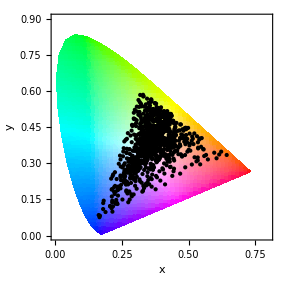

```mathematica
ChromaticityPlot[XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],1000],PlotStyle->Black]
```

We can try doing the same with interior colors.

```mathematica
innerColors=fruitInsideColorList[Interpreter["Food"][#]]&/@{"Apple","Orange","Carrot","Banana","Blueberry","Blackberry","Strawberry"};
XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],100]
```

{XYZColor[0.3771297739926417, 0.3381034840025122, 0.12395340595345306],XYZColor[0.370442492841068, 0.388542633722165, 0.13046183758764107],XYZColor[0.6465663249458654, 0.6504861273507115, 0.3343706377698762],XYZColor[0.7369717729833604, 0.7901352997346897, 0.3607475404482493],XYZColor[0.42446257766289774, 0.662118245890085, 0.18417549897448182],XYZColor[0.5500782818424951, 0.41297490702504114, 0.2710728673138353],XYZColor[0.49212969889878566, 0.38643769586702736, 0.3916045412770267],XYZColor[0.34372769683490334, 0.26473125617555426, 0.6108262299767916],XYZColor[0.36489834396691545, 0.42671827977934595, 0.13551701524999504],XYZColor[0.30933055446756275, 0.3472748590396514, 0.2428918276975428],XYZColor[0.6818543128437379, 0.8079181191547583, 0.4806102754763494],XYZColor[0.6218495323448762, 0.8053820319852231, 0.19408405851843902],XYZColor[0.4227509400054811, 0.4627996936004356, 0.30808544892282874],XYZColor[0.44960460666494095, 0.6185359215577159, 0.311066263781301],XYZColor[0.23820236546889484, 0.28553541400681703, 0.1867636538918539],XYZColor[0.3733116448391959, 0.36275521162264857, 0.2695192133472756],XYZColor[0.12827600578130005, 0.12366534565646303, 0.17912424104771685],XYZColor[0.6794025413457055, 0.8200286443467434, 0.25084462188770595],XYZColor[0.22674219172334442, 0.1786503295145675, 0.03863144147776021],XYZColor[0.43169676819231373, 0.4663304777402336, 0.39295104176859763],XYZColor[0.6109436613205551, 0.5874835363509042, 0.4980125337502449],XYZColor[0.6518859946443735, 0.621248627180148, 0.08294260365499861],XYZColor[0.5164335429994759, 0.5706987677884271, 0.4330981909714625],XYZColor[0.5040137386201596, 0.4913781513515264, 0.4207761063113328],XYZColor[0.3108616139133026, 0.23090250147275249, 0.6312335236751149],XYZColor[0.15855566559411172, 0.2519616187108288, 0.054268502384263395],XYZColor[0.408265892662082, 0.35604440585296426, 0.7038088403482826],XYZColor[0.656536422458666, 0.7514578981976167, 0.6019826084589374],XYZColor[0.4459269690423723, 0.4385794551389185, 0.2646775549282959],XYZColor[0.20473611984111229, 0.22477226594472566, 0.41219382429299667],XYZColor[0.5346922382152596, 0.5291082704861135, 0.5094685570644676],XYZColor[0.3542014561575032, 0.19391744223401275, 0.27070670060061197],XYZColor[0.6264925124120054, 0.6177010381401945, 0.14795770719606527],XYZColor[0.20495110414312434, 0.2550370016701463, 0.29886887014690433],XYZColor[0.3293719804643819, 0.46774193560718935, 0.1474341717063925],XYZColor[0.6349577895749822, 0.532873766193439, 0.3596379885150659],XYZColor[0.30355276733685843, 0.28425439787697593, 0.03245524626940455],XYZColor[0.18878474866997508, 0.2651215270887882, 0.15266070613653904],XYZColor[0.20435251294611, 0.12899640125071932, 0.30522840289227793],XYZColor[0.6787321350723402, 0.8293696964897211, 0.3263611761777886],XYZColor[0.45711229477050985, 0.6056667377668127, 0.09471722111900771],XYZColor[0.4954470927080784, 0.6114006914575217, 0.4776188149765982],XYZColor[0.400822418047328, 0.49055316083818556, 0.2392089258238973],XYZColor[0.8810368243052916, 0.9115512575005006, 0.7079351651726798],XYZColor[0.34054554832914674, 0.3540868393269444, 0.34421454475586677],XYZColor[0.5220138109605524, 0.4194355665091466, 0.15964623434935654],XYZColor[0.20561691161318552, 0.1995602571082532, 0.5306097714907766],XYZColor[0.10444407086667795, 0.05873826990667641, 0.44557749751032494],XYZColor[0.18967442155142444, 0.27600007081290545, 0.2312007193046023],XYZColor[0.355379192036409, 0.4836019964518291, 0.3539740135538777],XYZColor[0.407165097037392, 0.39283060942438397, 0.09736071765165244],XYZColor[0.4261296808713847, 0.5700541579376942, 0.3083724422439619],XYZColor[0.38242047324103845, 0.6416507275646842, 0.20007526396079822],XYZColor[0.2746265010290886, 0.20325492734141226, 0.16668339525153875],XYZColor[0.5903231505302234, 0.7725966317493954, 0.23534587089487669],XYZColor[0.28044030074879156, 0.21210167478482578, 0.5682242834823942],XYZColor[0.15366482893445543, 0.19069799366087647, 0.025999958913134003],XYZColor[0.3277631746134947, 0.37063685798065926, 0.36273371382957087],XYZColor[0.5868553806723097, 0.6540458222980373, 0.31872937479009],XYZColor[0.09484514491969354, 0.10544366068722344, 0.23910789541838884],XYZColor[0.4228487468181271, 0.4908701623363, 0.11765742470437557],XYZColor[0.6437634400237681, 0.7147399074525599, 0.4459867483828469],XYZColor[0.5467605700402886, 0.7164032831669181, 0.15166160741232249],XYZColor[0.6979310728197822, 0.6596473849254861, 0.29294744957022323],XYZColor[0.4554223635999547, 0.34626966866925446, 0.06373551625795548],XYZColor[0.3895568349075563, 0.6644056935264836, 0.18375105597951158],XYZColor[0.716460905075862, 0.7925661944395891, 0.18844067187188396],XYZColor[0.2956659394956208, 0.330478646090297, 0.11905498492964972],XYZColor[0.5899111004223211, 0.5779476939023215, 0.09485538910067748],XYZColor[0.4018387093245107, 0.3344383776985199, 0.21919469743865394],XYZColor[0.2793909368685009, 0.2393963127972868, 0.08086369651754743],XYZColor[0.6053334081680705, 0.6138274091587966, 0.3806982906574824],XYZColor[0.5131934730402364, 0.6365173733018433, 0.28745817292166376],XYZColor[0.7489558269425921, 0.8536511778819756, 0.22591435915003866],XYZColor[0.23167463934846066, 0.27642818089214616, 0.43376190984424545],XYZColor[0.7548120391948726, 0.7287631247886291, 0.40612617718019905],XYZColor[0.43262712032516026, 0.5762287538306757, 0.3347896365862951],XYZColor[0.22231737248074424, 0.16719694144900188, 0.30542042883750964],XYZColor[0.4015226359706533, 0.5678940581653177, 0.18193078222328507],XYZColor[0.5574993116457979, 0.6144608736939082, 0.47880881738572645],XYZColor[0.3167106974056745, 0.5426369896514353, 0.21916012023785314],XYZColor[0.7439598634810923, 0.8523742084853564, 0.19648135136081446],XYZColor[0.4927203006331985, 0.3374323600346899, 0.15317957772537572],XYZColor[0.7125776245154288, 0.786889105688486, 0.26096609599012843],XYZColor[0.5602139072548452, 0.6455680676811765, 0.14434549011837028],XYZColor[0.38574444338721336, 0.28406053329805536, 0.1270796897104165],XYZColor[0.33507326270588755, 0.2769105792925518, 0.6679957879844264],XYZColor[0.4251675124207085, 0.33763531494230914, 0.08177151488031564],XYZColor[0.7595807223095848, 0.8797134384241353, 0.10450628531599915],XYZColor[0.15523193808555613, 0.10586433692033925, 0.20579544870638966],XYZColor[0.2501271343898891, 0.27505957125817837, 0.5655623884786111],XYZColor[0.7777520762765401, 0.9093881290514624, 0.46640340252337353],XYZColor[0.2637024946355023, 0.2528777811401427, 0.03975868857411169],XYZColor[0.4437483766961142, 0.38486349102102924, 0.48133998565265046],XYZColor[0.6571297083551172, 0.601093674319615, 0.5795526200894391],XYZColor[0.38748612103279856, 0.3206186297197883, 0.4839918816204779],XYZColor[0.26452074519163105, 0.26292651336171546, 0.19174896837593025],XYZColor[0.7739282650422493, 0.8434830262819467, 0.6488659032274883],XYZColor[0.23337849886028905, 0.16410582901163207, 0.18528583039401403],XYZColor[0.45811395139593303, 0.5247264382038374, 0.3512093696987407]}

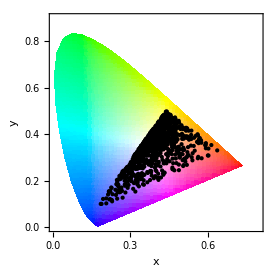

```mathematica
ChromaticityPlot[XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[innerColors,1]],1000],PlotStyle->Black]
```

The inside colors cover much less of the greens. Let’s combine these ingredients.

#### Mixture

Some appropriately colored apple slices:

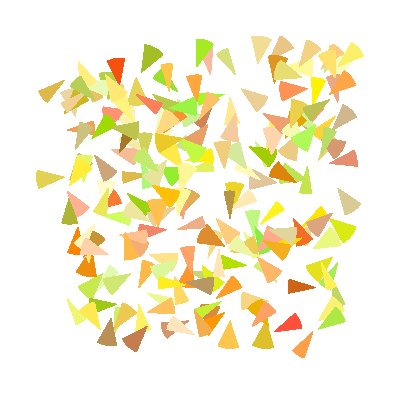

```mathematica
appleImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,1,{#[[1]],#[[1]]+#[[2]]}&@{RandomReal[{0,2Pi}],RandomReal[{Pi/8,Pi/4}]}]},200]]
```

Some carrot shavings:

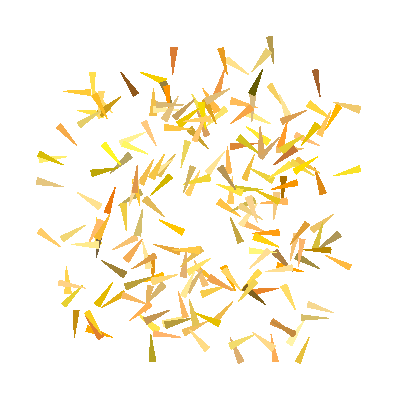

```mathematica
carrotImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,1,{#[[1]],#[[1]]+#[[2]]}&@{RandomReal[{0,2Pi}],RandomReal[{Pi/16,Pi/12}]}]},200]]
```

A few blueberries:

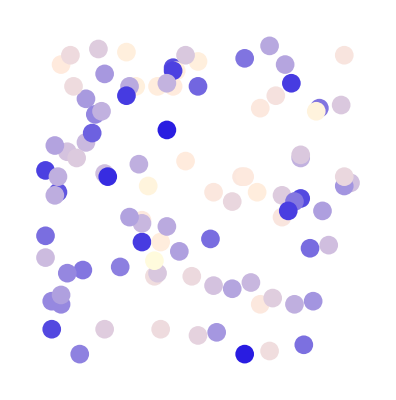

```mathematica
berryImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,0.3]},100]]
```

And the combination:

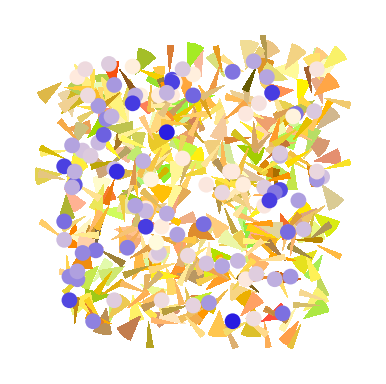

```mathematica
combo=Show[appleImage,carrotImage,berryImage]
```

Let’s put the ingredients in the blender to make our smoothie.

```mathematica
im=Rasterize[combo];
Manipulate[Blur[im,i],{i,2,50},SaveDefinitions->True]
```

Or we can cross the ingredients with a blender...

```mathematica
ImageRestyle[im,-Graphics-]
```

-Graphics-

This concludes our stroll through food data.